```mathematica
Lecture 12: Number Theory
```

## Divisors

### Exercise Subsection

Show that n^2 must have remainder 0, 1, or 4 modulo 5 (at least for the values of n up to 10^6).

```mathematica
DeleteDuplicates@Mod[Range[10^6]^2,5]
```

{1,4,0}

### Exercise Subsection

Show that the number 1111...1 (every digit of the integer is 1) must have remainder 3 modulo 4 (at least for the first 1000 integers of this form).

```mathematica
DeleteDuplicates@Mod[Table[Sum[10^n,{n,0,k}],{k,1,1000}],4]
```

{3}

### Exercise Subsection

Use ExtendedGCD to find integers x and y such that (2^100-1) x + (3^100-1) y == GCD[2^100-1, 3^100-1].

```mathematica
ExtendedGCD[2^100-1,3^100-1]
```

{138875,{-1162697940518182615500677620742689502959163,2859835136170798900894420}}

## Primes

### Exercise Subsection

Find a counterexample to the conjecture that if a positive integer n larger than 2 divides 2^n−2, then n is prime .

```mathematica
Select[Range[3,500],Divisible[2^#-2,#]&&CompositeQ@#&]
```

{341}

### Exercise Subsection

Let a, b, and c be the integers defined in the next cell.  Show that b and c are prime and that a is the product of b and c. 

While this exercise may not be difficult, it has historical significance.  The belief that nobody can factor integers quickly is the basis for some commonly used modern cryptographic systems.  From 1991 through 2007, the network security company RSA awarded prizes to anyone who could factor one of the integers on a list of challenge numbers.  The last challenge number that has been factored is the a below, which took over 3 years of computing time in 2009 (the command FactorInteger@a will probably take many years to run on your laptop!)

```mathematica
{a,b,c}={1230186684530117755130494958384962720772853569595334792197322452151726400507263657518745202199786469389956474942774063845925192557326303453731548268507917026122142913461670429214311602221240479274737794080665351419597459856902143413,33478071698956898786044169848212690817704794983713768568912431388982883793878002287614711652531743087737814467999489,36746043666799590428244633799627952632279158164343087642676032283815739666511279233373417143396810270092798736308917};
```

```mathematica
PrimeQ@{b,c}
```

{True,True}

```mathematica
a==b c
```

True

```mathematica
FactorInteger@a
```

$Aborted

### Exercise Subsection

The Riemann hypothesis is probably the most notorious unsolved problem in mathematics.  It is related to the distribution of primes.  There are many equivalent statements to the Riemann hypothesis, one says that the inequality in the next cell holds for values of n larger than 2657:

```mathematica
Abs[-NIntegrate[1/Log[t],{t,2,n}]+PrimePi[n]]≤(√n Log[n])/(8 π)
```

Show that the above inequality is true for all integers n larger than 3000 and less than 5000. 

Note: If you randomly select a large enough n and the above test happens to be False, then you have resolved the Riemann hypothesis in the negative and will earn a $1,000,000 prize.

```mathematica
Table[Abs[-NIntegrate[1/Log[t],{t,2,n}]+PrimePi[n]]≤(√n Log[n])/(8 π),{n,3000,5000}]//DeleteDuplicates
```

{True}

### Exercise Subsection

An open problem is to prove that there is always a prime between n^2 and (n+1)^2 for integers n larger than 2.  Verify this conjecture is true as the integer n range from 2 to 10^4.

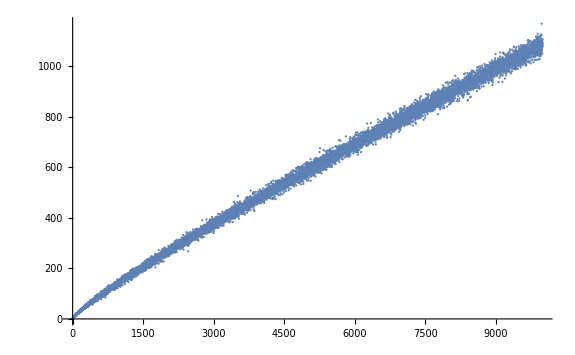

```mathematica
ListPlot[Table[PrimePi[(n+1)^2]-PrimePi[n^2],{n,2,10^4}]]
```

### Exercise Subsection

a. Create a function named PrimePositions[L_] which selects from L those elements in position 2, 3, 5, 7, 11,....  That is, return the elements in L that have a prime position in L.

```mathematica
{1,2,3,4,5}[[{1,3}]]
```

{1,3}

```mathematica
PrimePositions[L_]:=L[[Prime@Range@PrimePi@Length@L]]
```

```mathematica
PrimePositions[{3,10,2,1,4,7,"test"}]
```

{10,2,4,test}

b. The function SpiralSteps defined in the next cell

```mathematica
SpiralSteps[n_]:=If[n==0,{π/2,π/2},Join[SpiralSteps[n-1],{π/2},Table[0,n],{π/2},Table[0,n]]]
```

```mathematica
SpiralSteps[4]
```

{π/2,π/2,π/2,0,π/2,0,π/2,0,0,π/2,0,0,π/2,0,0,0,π/2,0,0,0,π/2,0,0,0,0,π/2,0,0,0,0}

defines a sequence of steps that can be used to create a spiral using AnglePath:

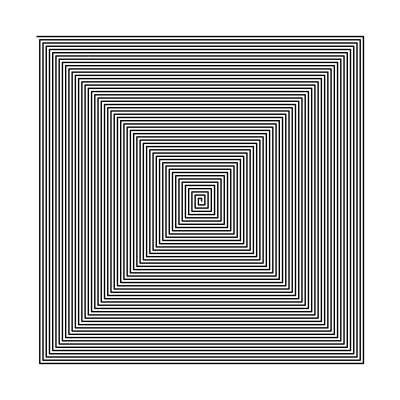

```mathematica
Graphics@Line@AnglePath@SpiralSteps@100
```

Use PrimePositions together with Graphics to place a Point at each coordinate in AnglePath@SpiralSteps@100 that is in a prime position.  The result is Ulam’s spiral (see https://en.wikipedia.org/wiki/Ulam_spiral ), which is interesting because so many points in the image lie on collinear diagonals.

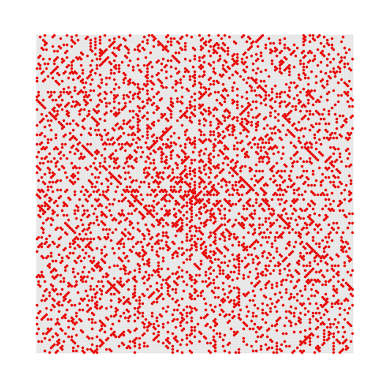
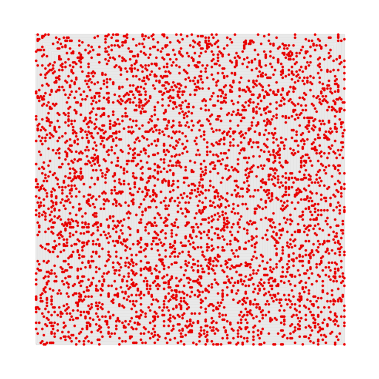

```mathematica
{Graphics[{Red,PointSize[.005],Point@PrimePositions@AnglePath@SpiralSteps@200,Black,Opacity[.1],Line@AnglePath@SpiralSteps@200}],
Graphics[{Red,PointSize[.005],Point@RandomSample[AnglePath@SpiralSteps@200,PrimePi@Length@SpiralSteps@200],Black,Opacity[.1],Line@AnglePath@SpiralSteps@200}]}
```

## Congruence equations

### Exercise Subsection

Equations (and systems of equations) can be solved working modulo m using the Modulus -> m option in Solve.  For example, solve the following equations working modulo 100, and then check that the answers are correct:

```mathematica
equation1=19x==1;
equation2={3 x+2y==4,2x+7y==6};
equation3={x^2+3 x y+y^2==1,2x^2-y==99};
equation4={{21,50,60,17,35},{29,40,9,42,34},{7,8,60,44,48},{97,6,38,9,90},{16,29,85,2,82}}.{a,b,c,d,e}=={1,2,3,4,5};
```

```mathematica
Mod[#,100]&/@{x^2+3 x y+y^2,2x^2-y}/.Solve[equation3,{x,y},Modulus->100]
```

{{1,99},{1,99},{1,99},{1,99},{1,99},{1,99},{1,99},{1,99},{1,99},{1,99},{1,99},{1,99},{1,99},{1,99}}

```mathematica
Clear[a,b,c,d,e]
```

```mathematica
Solve[equation4,{a,b,c,d,e},Modulus->100]
```

{{e→27,d→91,c→9,b→80,a→89}}

### Exercise Subsection

A multiplicative inverse to a modulo m is a solution to the equation a x == 1 modulo m.  Write a function MultInverse[a_,m_] that has input integers a and m and output {True, x} if x is the multiplicative inverse to a modulo m and {False} if no such x exists.

### Exercise Subsection

A woman with a basket of eggs finds that if she removes either 2, 3, 4, 5, or 6 at a time from the basket, there is always one egg left over . If she removes 7 eggs at a time from the basket, there are no eggs left over . What is the minimum number of eggs in the basket?  (Look up and use the function ChineseRemainder to solve this exercise.)

```mathematica
ChineseRemainder[{1,1,1,1,1,0},{2,3,4,5,6,7}]
```

301

### Exercise Subsection

The integer a between 0 and m-1 is a quadratic residue modulo m if there is at least one solution to the equation x^2 == a modulo m.  Write a function QuadraticResidue[m_] which produces a list of all quadratic residues modulo m.

```mathematica
QuadraticResidue[m_]:=Select[Range[0,m-1],Length@Solve[x^2==#,x,Modulus->m]!=0&]
```

## Number theoretic functions

### Exercise Subsection

EulerPhi is a function that has input a positive integer n and output equal to the number of positive integers smaller than n that are relatively prime to n.
a. Make a ListPlot of the first 1000 values of EulerPhi.

b. Find the least value of n such that EulerPhi gives the same output for n, n+1, and n+2.

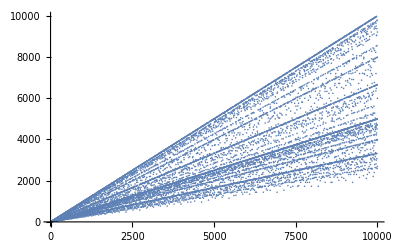

```mathematica
ListPlot[EulerPhi/@Range@10000]
```

```mathematica
n=1;
While[EulerPhi@n!=EulerPhi[n+1]||EulerPhi[n]!=EulerPhi[n+2],n=n+1]
n
```

5186

```mathematica
EulerPhi[n+2]
```

2592

### Exercise Subsection

```mathematica
PrimeOmega[20]
```

3

a. The function PrimeOmega[n] gives the number of primes that divide n, counting multiplicities.  Create a list of length 20 such that element i on the list is the number of times an integer n between 1 and 10^5 has PrimeOmega[n] equal to i.  Then use ListPlot on this list to see the distribution of PrimeOmega[n] for values of n between 1 and 10^5.

b. Using the function

```mathematica
SpiralSteps[n_]:=If[n==0,{π/2,π/2},Join[SpiralSteps[n-1],{π/2},Table[0,n],{π/2},Table[0,n]]]
```

defined in a previous exercise, the next line defines a graphic that places a point with a radius that depends on PrimeOmega at each point along the spiral.  Admire the graphic!  That’s all you need to do: admire it!

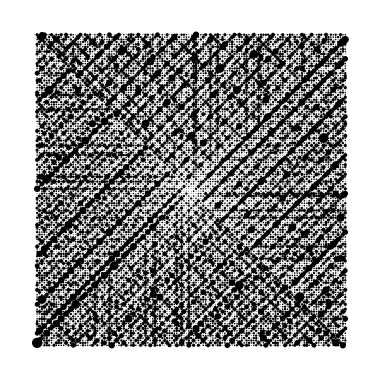

```mathematica
Graphics@Module[{steps=AnglePath@SpiralSteps@128},Table[{PointSize[0.0015*(PrimeOmega@i-1)],Point@steps[[i]]},{i,Length@steps}]]
```

### Exercise Subsection

The function Zeta[s] gives the Riemann zeta function at the complex number s.  This function is related to the distribution of prime numbers.  

a. Find the first 10 terms in the Series expansion of 1/Zeta[s] centered at s=5, using N to approximate the coefficients.  Then show this is very close to the series centered at s=5 for the function in the next cell.

```mathematica
(1-2^-s) (1-3^-s) (1-5^-s) (1-7^-s) (1-11^-s) (1-13^-s) (1-17^-s) (1-19^-s) (1-23^-s) (1-29^-s)
```

b. Simplify the infinite sum of terms of the form EulerPhi[n]/n^s as n ranges from 1 to Infinity to find an expression involving the Zeta function.

### Exercise Subsection

Find at least 10 values of n such that EulerPhi[DivisiorSigma[1,n]] is equal to n.